```mathematica
ResetContextPath[ ];
ClearAll[ "Global`*" ];

Block[ { $ContextPath },
    Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
    TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
]
```

TestReportObject[…]

### Basic Examples

Create an AST pattern that will match any CallNode or LeafNode generated by CodeParse:

```mathematica
ASTPattern[_]
```

(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]

Specify a head:

```mathematica
ASTPattern[_head]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,head|Global`head,_],_,_]

A function with two arguments:

```mathematica
ASTPattern[f[_,_]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

A function with any number of arguments:

```mathematica
ASTPattern[f[___]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]...},_]

A named Pattern:

```mathematica
ASTPattern[a_Integer]
```

a:(CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_]

A Repeated pattern:

```mathematica
ASTPattern[{(_Integer?IntegerQ|_String?StringQ)..}]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,List|System`List,_],{(CodeParser`LeafNode[Integer,_,_]|CodeParser`LeafNode[String,_,_])..},_]

A Verbatim pattern:

```mathematica
ASTPattern[Verbatim[_Integer]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,Blank|System`Blank,_],{CodeParser`LeafNode[Symbol,Integer|System`Integer,_]},_]

A PatternSequence:

```mathematica
ASTPattern[{___,PatternSequence[x,y],___}]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,List|System`List,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]...,PatternSequence[CodeParser`LeafNode[Symbol,x|Global`x,_],CodeParser`LeafNode[Symbol,y|Global`y,_]],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]...},_]

A pattern for unevaluated code wrapped in HoldPattern:

```mathematica
ASTPattern[HoldPattern[1+1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus|System`Plus,_],{CodeParser`LeafNode[Integer,1,_],CodeParser`LeafNode[Integer,1,_]},_]

A PatternTest:

```mathematica
ASTPattern[_?test]
```

((CodeParser`CallNode|CodeParser`LeafNode)[_,_,_])?test

A Condition:

```mathematica
ASTPattern[a_/;test[a]]
```

a:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]/;test[a]

Duplicate pattern bindings:

```mathematica
ASTPattern[{a_,a_,a_}]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,List|System`List,_],{a:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],a$14885:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],a$14886:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]/;a≃a$14885≃a$14886

Nested patterns:

```mathematica
ASTPattern[expr:f[_,ASTPattern[arg_],_]]
```

expr:CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],arg:(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

### Scope

Use the second argument of ASTPattern to match node metadata:

```mathematica
Cases[CodeParser`CodeParse["f[x_]:=x+y;\ny=1;"],ASTPattern[_,KeyValuePattern["Definitions"->defs_]]:>defs,Infinity]
```

{{CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,1},{1,2}}|>]},{CodeParser`LeafNode[Symbol,y,<|CodeParser`Source→{{2,1},{2,2}}|>]}}

Match only nodes that start on a particular line:

```mathematica
Cases[CodeParser`CodeParse["1+1\n2+2\n3+3"],ASTPattern[_,KeyValuePattern[CodeParser`Source->{{2,_},_}]],Infinity]
```

{CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,1},{2,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,3},{2,4}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus,<||>],{CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,1},{2,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{2,3},{2,4}}|>]},<|CodeParser`Source→{{2,1},{2,4}}|>]}

Bind parts of metadata in pattern names:

```mathematica
ast=CodeParser`CodeParse["1+1"]
```

CodeParser`ContainerNode[String,{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus,<||>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>],CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,3},{1,4}}|>]},<|CodeParser`Source→{{1,1},{1,4}}|>]},<||>]

```mathematica
rule=ASTPattern[node_Plus,meta:KeyValuePattern[CodeParser`Source->src_]]:><|"String"->CodeParser`ToFullFormString[node],"Source"->src,"Metadata"->meta|>
```

node:CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus|System`Plus,_],_,meta:KeyValuePattern[CodeParser`Source→src_]]:>Association[String→CodeParser`ToFullFormString[node],Source→src,Metadata→meta]

```mathematica
Cases[ast,rule,Infinity]
```

{<|String→Plus[1, 1],Source→{{1,1},{1,4}},Metadata→<|CodeParser`Source→{{1,1},{1,4}}|>|>}

### Options

### Applications

Parse a Wolfram Language file to get an abstract syntax tree:

```mathematica
Short[ast=CodeParser`CodeParse[File["ExampleData/Collatz.m"],"SourceConvention"->"SourceCharacterIndex"]]
```

CodeParser`ContainerNode[File,{CodeParser`PackageNode[{CodeParser`LeafNode[String,"Collatz`",<|CodeParser`Source→{14,23}|>]},{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Set,<||>],{CodeParser`CallNode[«1»],«1»},<|CodeParser`Source→{27,202},Definitions→{CodeParser`LeafNode[Symbol,Collatz,<|CodeParser`Source→{27,33}|>]}|>],CodeParser`ContextNode[«1»]},<|CodeParser`Source→{1,406}|>]},<|CodeParser`Source→{1,406},FileName→C:\Program Files\Wolfram Research\Mathematica\13.0\Documentation\English\System\ExampleData\Collatz.m|>]

Extract all nodes from the AST that correspond to a pattern:

```mathematica
nodes=Cases[ast,ASTPattern[Collatz[_Plus|_Times]],Infinity]
```

{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Collatz,<|CodeParser`Source→{275,281}|>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus,<||>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Times,<||>],{CodeParser`LeafNode[Integer,3,<|CodeParser`Source→{283,283}|>],CodeParser`LeafNode[Symbol,n,<|CodeParser`Source→{285,285}|>]},<|CodeParser`Source→{283,285}|>],CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{289,289}|>]},<|CodeParser`Source→{283,289}|>]},<|CodeParser`Source→{275,290}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,Collatz,<|CodeParser`Source→{347,353}|>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Times,<||>],{CodeParser`LeafNode[Symbol,n,<|CodeParser`Source→{355,355}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,Power,<||>],{CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{357,357}|>],CodeParser`LeafNode[Integer,-1,<||>]},<|CodeParser`Source→{355,357}|>]},<|CodeParser`Source→{355,357}|>]},<|CodeParser`Source→{347,358}|>]}

Convert to expressions:

```mathematica
ToExpression[CodeParser`ToFullFormString/@nodes,InputForm,Hold]
```

{Hold[Collatz[3 n+1]],Hold[Collatz[n/2]]}

Extract source positions:

```mathematica
pos=Cases[ast,ASTPattern[Collatz[_],KeyValuePattern[CodeParser`Source->src_]]:>src,Infinity]
```

{{225,234},{244,261},{275,290},{317,334},{347,358}}

Extract the corresponding parts of the file as strings:

```mathematica
StringTake[ReadString["ExampleData/Collatz.m"],pos]
```

{Collatz[1],Collatz[n_Integer],Collatz[3 n + 1],Collatz[n_Integer],Collatz[n/2]}

Create a CodeCases function:

```mathematica
CodeCases[file_File,patt_]:=CodeCases[ReadString[file],patt];
CodeCases[string_String,patt_]:=StringTake[string,Cases[CodeParser`CodeParse[string,"SourceConvention"->"SourceCharacterIndex"],ASTPattern[patt,KeyValuePattern[CodeParser`Source->src_]]:>src,Infinity]];
```

```mathematica
CodeCases[File["ExampleData/Collatz.m"],_Collatz]
```

{Collatz[1],Collatz[n_Integer],Collatz[3 n + 1],Collatz[n_Integer],Collatz[n/2]}

Compare to string matching:

```mathematica
StringCases[ReadString["ExampleData/Collatz.m"],Shortest["Collatz["~~___~~"]"]]
```

{Collatz[n],Collatz[1],Collatz[n_Integer],Collatz[3 n + 1],Collatz[n_Integer],Collatz[n/2]}

This incorrectly matched part of the usage message as code:

```mathematica
ReadString["ExampleData/Collatz.m"]
```

BeginPackage["Collatz`"]

Collatz::usage =
        "Collatz[n] gives a list of the iterates in the 3n+1 problem,
        starting from n. The conjecture is that this sequence always
        terminates."

Begin["`Private`"]

Collatz[1] := {1}

Collatz[n_Integer]  := Prepend[Collatz[3 n + 1], n] /; OddQ[n] && n > 0

Collatz[n_Integer] := Prepend[Collatz[n/2], n] /; EvenQ[n] && n > 0

End[ ]

EndPackage[ ]

When matching against the AST, there's no need to account for different types of input syntax:

```mathematica
CodeCases[File["ExampleData/Collatz.m"],And[_,_]]
```

{OddQ[n] && n > 0,EvenQ[n] && n > 0}

### Properties and Relations

The single-argument form of ASTPattern is effectively invisible to an outer ASTPattern:

```mathematica
ASTPattern[f[ASTPattern[_],ASTPattern[_]]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

```mathematica
ASTPattern[f[_,_]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,_]},_]

```mathematica
%===%%
```

True

The two-argument form inserts the corresponding metadata patterns:

```mathematica
ASTPattern[f[ASTPattern[_,a_],ASTPattern[_,b_]],c_]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[_,_,a_],(CodeParser`CallNode|CodeParser`LeafNode)[_,_,b_]},c_]

Get an AST node corresponding to a simple expression:

```mathematica
node=CodeParser`CodeParse["f[1]"][[2,1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,1},{1,2}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,3},{1,4}}|>]},<|CodeParser`Source→{{1,1},{1,5}}|>]

For simple patterns, the performance of matching an ASTPattern is comparable to normal pattern matching:

```mathematica
simple=ASTPattern[f[_Integer]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{(CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_]},_]

```mathematica
RepeatedTiming[MatchQ[node,simple]]
```

{3.21499×10^-7,True}

```mathematica
RepeatedTiming[MatchQ[f[1],f[_Integer]]]
```

{1.19974×10^-7,True}

Matching patterns that require evaluation typically incur significant cost as an ASTPattern:

```mathematica
patt=ASTPattern[f[x_Integer/;IntegerQ[x]]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{x:(CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_]/;IntegerQ[x]},_]

```mathematica
RepeatedTiming[MatchQ[node,patt]]
```

{0.0000164776,True}

Compare to normal pattern matching:

```mathematica
RepeatedTiming[MatchQ[f[1],f[x_Integer/;IntegerQ[x]]]]
```

{2.81459×10^-7,True}

Some pattern tests allow for optimized patterns:

```mathematica
ASTPattern[_Integer?IntegerQ]
```

CodeParser`LeafNode[Integer,_,_]

```mathematica
ASTPattern[_Integer?AtomQ]
```

CodeParser`LeafNode[Integer,_,_]

```mathematica
ASTPattern[_String?StringQ]
```

CodeParser`LeafNode[String,_,_]

```mathematica
ASTPattern[_String?AtomQ]
```

CodeParser`LeafNode[String,_,_]

This will only work for certain pattern tests that appear literally:

```mathematica
myIntegerQ=IntegerQ;
ASTPattern[_Integer?myIntegerQ]
```

((CodeParser`CallNode|CodeParser`LeafNode)[Integer|CodeParser`LeafNode[Symbol,Integer|System`Integer,_],_,_])?myIntegerQ

Pattern bindings that stay within ASTPattern correspond to expressions:

```mathematica
ast=CodeParser`CodeParse["1+2"];
Cases[ast,ASTPattern[x_Integer/;(Echo[x,"Inside"]; True)],Infinity]
```

Inside  1

Inside  2

{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{1,3},{1,4}}|>]}

Once a value passes outside of ASTPattern, the binding corresponds to the AST node:

```mathematica
Cases[ast,ASTPattern[x_Integer]/;(Echo[x,"Outside"]; True),Infinity]
```

Outside  CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>]

Outside  CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{1,3},{1,4}}|>]

{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,1},{1,2}}|>],CodeParser`LeafNode[Integer,2,<|CodeParser`Source→{{1,3},{1,4}}|>]}

Note that all instances of the pattern symbol appear below ASTPattern in this case:

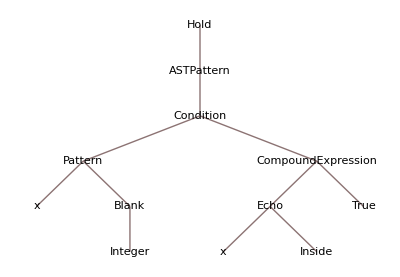

```mathematica
TreeForm[Hold[ASTPattern[x_Integer/;(Echo[x,"Inside"]; True)]]]
```

In this case, there is an x that's "lifted" out of the ASTPattern, which is why it appears as an AST node:

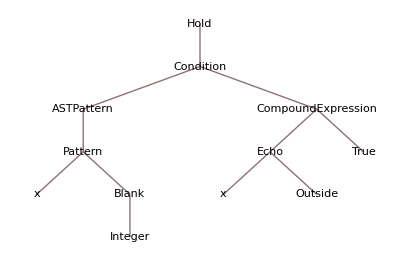

```mathematica
TreeForm[Hold[ASTPattern[x_Integer]/;(Echo[x,"Outside"]; True)]]
```

### Possible Issues

ASTPattern cannot generalize to all possible WL patterns:

```mathematica
ast=CodeParser`CodeParse["{f[1],f[1],f[1]}"]
```

CodeParser`ContainerNode[String,{CodeParser`CallNode[CodeParser`LeafNode[Symbol,List,<||>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,2},{1,3}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,4},{1,5}}|>]},<|CodeParser`Source→{{1,2},{1,6}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,7},{1,8}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,9},{1,10}}|>]},<|CodeParser`Source→{{1,7},{1,11}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,12},{1,13}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,14},{1,15}}|>]},<|CodeParser`Source→{{1,12},{1,16}}|>]},<|CodeParser`Source→{{1,1},{1,17}}|>]},<||>]

```mathematica
FreeQ[ast,ASTPattern[{f[a_]..}]]
```

True

```mathematica
FreeQ[{f[1],f[1],f[1]},{f[a_]..}]
```

False

In this case, the pattern binding prevents matching, since the metadata will always be different between nodes:

```mathematica
Cases[ast,ASTPattern[{f[_]..}],Infinity]
```

{CodeParser`CallNode[CodeParser`LeafNode[Symbol,List,<||>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,2},{1,3}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,4},{1,5}}|>]},<|CodeParser`Source→{{1,2},{1,6}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,7},{1,8}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,9},{1,10}}|>]},<|CodeParser`Source→{{1,7},{1,11}}|>],CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,12},{1,13}}|>],{CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,14},{1,15}}|>]},<|CodeParser`Source→{{1,12},{1,16}}|>]},<|CodeParser`Source→{{1,1},{1,17}}|>]}

```mathematica
%[[1,2,All,3]]
```

{<|CodeParser`Source→{{1,2},{1,6}}|>,<|CodeParser`Source→{{1,7},{1,11}}|>,<|CodeParser`Source→{{1,12},{1,16}}|>}

Without any repeated binding this pattern will match:

```mathematica
FreeQ[ast,ASTPattern[{f[_]..}]]
```

False

Not all raw patterns are supported by ASTPattern:

```mathematica
node=CodeParser`CodeParse["f[x -> 1]"][[2,1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f,<|CodeParser`Source→{{1,1},{1,2}}|>],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,Rule,<||>],{CodeParser`LeafNode[Symbol,x,<|CodeParser`Source→{{1,3},{1,4}}|>],CodeParser`LeafNode[Integer,1,<|CodeParser`Source→{{1,8},{1,9}}|>]},<|CodeParser`Source→{{1,3},{1,9}}|>]},<|CodeParser`Source→{{1,1},{1,10}}|>]

```mathematica
patt=ASTPattern[f[OptionsPattern[]]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,f|Global`f,_],{CodeParser`CallNode[CodeParser`LeafNode[Symbol,OptionsPattern|System`OptionsPattern,_],{},_]},_]

```mathematica
MatchQ[node,patt]
```

False

```mathematica
MatchQ[f[x->1],f[OptionsPattern[]]]
```

True

Unsupported patterns are represented verbatim:

```mathematica
MatchQ[CodeParser`CodeParse["f[OptionsPattern[]]"][[2,1]],patt]
```

True

```mathematica
MatchQ[f[OptionsPattern[]],Verbatim[f[OptionsPattern[]]]]
```

True

ASTPattern ignores the Unevaluated wrapper:

```mathematica
patt=ASTPattern[Unevaluated[1+1]]
```

CodeParser`LeafNode[Integer,2,_]

```mathematica
FreeQ[CodeParser`CodeParse["Hold[1+1]"],patt]
```

True

Use HoldPattern instead:

```mathematica
patt=ASTPattern[HoldPattern[1+1]]
```

CodeParser`CallNode[CodeParser`LeafNode[Symbol,Plus|System`Plus,_],{CodeParser`LeafNode[Integer,1,_],CodeParser`LeafNode[Integer,1,_]},_]

```mathematica
FreeQ[CodeParser`CodeParse["Hold[1+1]"],patt]
```

False

ASTPattern must evaluate in order to create the desired pattern, so it should not be wrapped in HoldPattern:

```mathematica
MatchQ[CodeParser`CodeParse["1+1"][[2,1]],HoldPattern[ASTPattern[1+1]]]
```

False

Use HoldPattern within ASTPattern instead:

```mathematica
MatchQ[CodeParser`CodeParse["1+1"][[2,1]],ASTPattern[HoldPattern[1+1]]]
```

True

### Neat Examples